## En dan

```mathematica
letter="e";
```

```mathematica
colofour="colofourTest";
```

```mathematica
Table[With[{g=allGraphs5[k,"graph"]},If[VertexCount[g]==4||VertexCount[g]==3,ShowGraph5Least[Convert[k]],ShowGraph5Least[k]]],{k,allGraphs5NullAtomKeys}]
```

{-Graphics-034,-Graphics-492070,-Graphics-560111,-Graphics-575282,-Graphics-590481,-Graphics-544922,-Graphics-529762,-Graphics-514750,-Graphics-454162,-Graphics-439081,-Graphics-499631,-Graphics-408962,-Graphics-492161,-Graphics-393922,-Graphics-492100,-Graphics-492081,-Graphics-360850,-Graphics-382810,-Graphics-189802,-Graphics-175681,-Graphics-368170,-Graphics-147481,-Graphics-361660,-Graphics-133401,-Graphics-361120,-Graphics-360860,-Graphics-317110,-Graphics-324411,-Graphics-63202,-Graphics-319540,-Graphics-49201,-Graphics-317380,-Graphics-317140,-Graphics-302530,-Graphics-304961,-Graphics-21242,-Graphics-303340,-Graphics-302621,-Graphics-297670,-Graphics-298571,-Graphics-7282,-Graphics-297970,-Graphics-297681,-Graphics-296050,-Graphics-296330,-Graphics-296080,-Graphics-295510,-Graphics-295600,-Graphics-295330,-Graphics-295371,-Graphics-295270,-Graphics-295250}

```mathematica
sets123=Table[With[{g=allGraphs5[k,"graph"]},If[VertexCount[g]==4||VertexCount[g]==3,Convert[k],k]],{k,allGraphs5NullAtomKeys}]
```

{0,49207,56011,57528,59048,54492,52976,51475,45416,43908,49963,40896,49216,39392,49210,49208,36085,38281,18980,17568,36817,14748,36166,13340,36112,36086,31711,32441,6320,31954,4920,31738,31714,30253,30496,2124,30334,30262,29767,29857,728,29797,29768,29605,29633,29608,29551,29560,29533,29537,29527,29525}

```mathematica
Table[With[{g=allGraphs5[k,"graph"]},If[VertexCount[g]==5,ShowGraph5Least[Convert[k]],ShowGraph5Least[k]]],{k,sets123}]
```

{-Graphics-295240,-Graphics-492070,-Graphics-560111,-Graphics-575282,-Graphics-590481,-Graphics-544922,-Graphics-529762,-Graphics-514750,-Graphics-454162,-Graphics-439081,-Graphics-499631,-Graphics-408962,-Graphics-492161,-Graphics-393922,-Graphics-492100,-Graphics-492081,-Graphics-360850,-Graphics-382810,-Graphics-189802,-Graphics-175681,-Graphics-368170,-Graphics-147481,-Graphics-361660,-Graphics-133401,-Graphics-361120,-Graphics-360860,-Graphics-317110,-Graphics-324411,-Graphics-63202,-Graphics-319540,-Graphics-49201,-Graphics-317380,-Graphics-317140,-Graphics-302530,-Graphics-304961,-Graphics-21242,-Graphics-303340,-Graphics-302621,-Graphics-297670,-Graphics-298571,-Graphics-7282,-Graphics-297970,-Graphics-297681,-Graphics-296050,-Graphics-296330,-Graphics-296080,-Graphics-295510,-Graphics-295600,-Graphics-295330,-Graphics-295371,-Graphics-295270,-Graphics-295250}

```mathematica
Table[SetsToSymbol[allGraphs5[k,"vertexsets"],letter],{k,sets123}]
```

{e1x2x3x4x5,e12x3x4x5,e123x4x5,e1234x5,e12345,e1235x4,e123x45,e124x3x5,e1245x3,e124x35,e125x3x4,e125x34,e12x34x5,e12x345,e12x35x4,e12x3x45,e13x2x4x5,e134x2x5,e1345x2,e134x25,e135x2x4,e135x24,e13x24x5,e13x245,e13x25x4,e13x2x45,e14x2x3x5,e145x2x3,e145x23,e14x23x5,e14x235,e14x25x3,e14x2x35,e15x2x3x4,e15x23x4,e15x234,e15x24x3,e15x2x34,e1x23x4x5,e1x234x5,e1x2345,e1x235x4,e1x23x45,e1x24x3x5,e1x245x3,e1x24x35,e1x25x3x4,e1x25x34,e1x2x34x5,e1x2x345,e1x2x35x4,e1x2x3x45}

```mathematica
rep123=First[Solve[Fold[And,Table[SetsToSymbol[allGraphs5[k,"vertexsets"],letter]==allGraphs5[Convert[k],"colofour"],{k,sets123}]],Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]]];
```

```mathematica
rep123
```

{v1x2x3x4x5→e1x2x3x4x5,v1x2x3x45→5 e12345+2 e123x45+2 e1245x3+e12x345-e12x3x45+2 e1345x2+e13x245-e13x2x45+e145x23-e145x2x3+2 e1x2345-e1x23x45-e1x245x3-e1x2x345+e1x2x3x45,v1x2x35x4→5 e12345+2 e1235x4+2 e124x35+e12x345-e12x35x4+2 e1345x2+e135x24-e135x2x4+e14x235-e14x2x35+2 e1x2345-e1x235x4-e1x24x35-e1x2x345+e1x2x35x4,v1x2x34x5→5 e12345+2 e1234x5+2 e125x34+e12x345-e12x34x5+2 e1345x2+e134x25-e134x2x5+e15x234-e15x2x34+2 e1x2345-e1x234x5-e1x25x34-e1x2x345+e1x2x34x5,v1x2x345→-e12345-e12x345-e1345x2-e1x2345+e1x2x345,v1x25x3x4→5 e12345+2 e1235x4+2 e1245x3+e125x34-e125x3x4+2 e134x25+e13x245-e13x25x4+e14x235-e14x25x3+2 e1x2345-e1x235x4-e1x245x3-e1x25x34+e1x25x3x4,v1x25x34→-e12345-e125x34-e134x25-e1x2345+e1x25x34,v1x24x3x5→5 e12345+2 e1234x5+2 e1245x3+e124x35-e124x3x5+2 e135x24+e13x245-e13x24x5+e15x234-e15x24x3+2 e1x2345-e1x234x5-e1x245x3-e1x24x35+e1x24x3x5,v1x24x35→-e12345-e124x35-e135x24-e1x2345+e1x24x35,v1x245x3→-e12345-e1245x3-e13x245-e1x2345+e1x245x3,v1x23x4x5→5 e12345+2 e1234x5+2 e1235x4+e123x45-e123x4x5+2 e145x23+e14x235-e14x23x5+e15x234-e15x23x4+2 e1x2345-e1x234x5-e1x235x4-e1x23x45+e1x23x4x5,v1x23x45→-e12345-e123x45-e145x23-e1x2345+e1x23x45,v1x235x4→-e12345-e1235x4-e14x235-e1x2345+e1x235x4,v1x234x5→-e12345-e1234x5-e15x234-e1x2345+e1x234x5,v1x2345→e1x2345,v15x2x3x4→5 e12345+2 e1235x4+2 e1245x3+e125x34-e125x3x4+2 e1345x2+e135x24-e135x2x4+e145x23-e145x2x3+2 e15x234-e15x23x4-e15x24x3-e15x2x34+e15x2x3x4,v15x2x34→-e12345-e125x34-e1345x2-e15x234+e15x2x34,v15x24x3→-e12345-e1245x3-e135x24-e15x234+e15x24x3,v15x23x4→-e12345-e1235x4-e145x23-e15x234+e15x23x4,v15x234→e15x234,v14x2x3x5→5 e12345+2 e1234x5+2 e1245x3+e124x35-e124x3x5+2 e1345x2+e134x25-e134x2x5+e145x23-e145x2x3+2 e14x235-e14x23x5-e14x25x3-e14x2x35+e14x2x3x5,v14x2x35→-e12345-e124x35-e1345x2-e14x235+e14x2x35,v14x25x3→-e12345-e1245x3-e134x25-e14x235+e14x25x3,v14x23x5→-e12345-e1234x5-e145x23-e14x235+e14x23x5,v14x235→e14x235,v145x2x3→-e12345-e1245x3-e1345x2-e145x23+e145x2x3,v145x23→e145x23,v13x2x4x5→5 e12345+2 e1234x5+2 e1235x4+e123x45-e123x4x5+2 e1345x2+e134x25-e134x2x5+e135x24-e135x2x4+2 e13x245-e13x24x5-e13x25x4-e13x2x45+e13x2x4x5,v13x2x45→-e12345-e123x45-e1345x2-e13x245+e13x2x45,v13x25x4→-e12345-e1235x4-e134x25-e13x245+e13x25x4,v13x24x5→-e12345-e1234x5-e135x24-e13x245+e13x24x5,v13x245→e13x245,v135x2x4→-e12345-e1235x4-e1345x2-e135x24+e135x2x4,v135x24→e135x24,v134x2x5→-e12345-e1234x5-e1345x2-e134x25+e134x2x5,v134x25→e134x25,v1345x2→e1345x2,v12x3x4x5→5 e12345+2 e1234x5+2 e1235x4+e123x45-e123x4x5+2 e1245x3+e124x35-e124x3x5+e125x34-e125x3x4+2 e12x345-e12x34x5-e12x35x4-e12x3x45+e12x3x4x5,v12x3x45→-e12345-e123x45-e1245x3-e12x345+e12x3x45,v12x35x4→-e12345-e1235x4-e124x35-e12x345+e12x35x4,v12x34x5→-e12345-e1234x5-e125x34-e12x345+e12x34x5,v12x345→e12x345,v125x3x4→-e12345-e1235x4-e1245x3-e125x34+e125x3x4,v125x34→e125x34,v124x3x5→-e12345-e1234x5-e1245x3-e124x35+e124x3x5,v124x35→e124x35,v1245x3→e1245x3,v123x4x5→-e12345-e1234x5-e1235x4-e123x45+e123x4x5,v123x45→e123x45,v1235x4→e1235x4,v1234x5→e1234x5,v12345→e12345}

```mathematica
Monitor[Table[allGraphs5[k,colofour]=Simplify[(allGraphs5[k,"colofour"]/.rep123)],{k,Keys[allGraphs5]}],k]
```

{26 e12345+6 e1234x5+6 e1235x4+2 e123x45-2 e123x4x5+6 e1245x3+2 e124x35-2 e124x3x5+2 e125x34-2 e125x3x4+2 e12x345-e12x34x5-e12x35x4-e12x3x45+e12x3x4x5+6 e1345x2+2 e134x25-2 e134x2x5+2 e135x24-2 e135x2x4+2 e13x245-e13x24x5-e13x25x4-e13x2x45+e13x2x4x5+2 e145x23-2 e145x2x3+2 e14x235-e14x23x5-e14x25x3-e14x2x35+e14x2x3x5+2 e15x234-e15x23x4-e15x24x3-e15x2x34+e15x2x3x4+6 e1x2345-2 e1x234x5-2 e1x235x4-e1x23x45+e1x23x4x5-2 e1x245x3-e1x24x35+e1x24x3x5-e1x25x34+e1x25x3x4-2 e1x2x345+e1x2x34x5+e1x2x35x4+e1x2x3x45+e1x2x3x4x5,1893,e1x2x3x45}
 |  |  |  |

```mathematica
Bases=Block[{result},
result=Association[];
result["C"]=Association[];
result["C","Colofour"]="colofour";
result["E"]=Association[];
result["E","Colofour"]="colofourrealnull";
result["G"]=Association[];
result["G","Colofour"]="colofourgenerator";
result["F"]=Association[];
result["F","Colofour"]="colofournull";
result["T"]=Association[];
result["T","Colofour"]="colotree";
result["Z"]=Association[];
result["Z","Colofour"]="colotreejef";
result["X"]=Association[];
result["X","Colofour"]="colotreepol";
result[letter]=Association[];
result[letter,"Colofour"]=colofour;
Table[result[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,result[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,result[base,"Colofour"]],allGraphs5[#2,result[base,"Colofour"]]]&]
,{base,Keys[result]}];
Table[result[base,"Variables"]=Table[allGraphs5[k,result[base,"Colofour"]],{k,result[base,"AtomKeys"]}]
,{base,Keys[result]}];
result
]
```

<|C→<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>,E→<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>,G→<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>,F→<|Colofour→colofournull,AtomKeys→{0,19683,6561,2187,729,243,81,27,9,3,1,26487,21951,20439,19692,19686,19684,8757,7293,6642,6588,6562,2917,2430,2214,2190,972,810,738,333,273,244,109,84,36,13,28764,27246,26488,22708,21954,20448,19696,9490,8784,7374,6670,3160,2460,1062,364,29524},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,T→<|Colofour→colotree,AtomKeys→{19936,46180,33130,24384,21420,26821,22287,20721,20029,19969,19940,55252,50718,47694,48460,46942,46184,37548,34620,35434,33916,33158,25868,31224,25168,24414,28308,23770,21510,29128,27610,26852,23072,22318,20812,20060,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{t1x2x3x4x5,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t1x2x34x5,t1x2x35x4,t1x2x3x45,t123x4x5,t124x3x5,t125x3x4,t12x34x5,t12x35x4,t12x3x45,t134x2x5,t135x2x4,t13x24x5,t13x25x4,t13x2x45,t145x2x3,t14x23x5,t14x25x3,t14x2x35,t15x23x4,t15x24x3,t15x2x34,t1x234x5,t1x235x4,t1x23x45,t1x245x3,t1x24x35,t1x25x34,t1x2x345,t1234x5,t1235x4,t123x45,t1245x3,t124x35,t125x34,t12x345,t1345x2,t134x25,t135x24,t13x245,t145x23,t14x235,t15x234,t1x2345,t12345}|>,Z→<|Colofour→colotreejef,AtomKeys→{29524,39366,13122,4374,1458,486,162,54,18,6,2,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{z1x2x3x4x5,z12x3x4x5,z13x2x4x5,z14x2x3x5,z15x2x3x4,z1x23x4x5,z1x24x3x5,z1x25x3x4,z1x2x34x5,z1x2x35x4,z1x2x3x45,z123x4x5,z124x3x5,z125x3x4,z12x34x5,z12x35x4,z12x3x45,z134x2x5,z135x2x4,z13x24x5,z13x25x4,z13x2x45,z145x2x3,z14x23x5,z14x25x3,z14x2x35,z15x23x4,z15x24x3,z15x2x34,z1x234x5,z1x235x4,z1x23x45,z1x245x3,z1x24x35,z1x25x34,z1x2x345,z1234x5,z1235x4,z123x45,z1245x3,z124x35,z125x34,z12x345,z1345x2,z134x25,z135x24,z13x245,z145x23,z14x235,z15x234,z1x2345,z12345}|>,X→<|Colofour→colotreepol,AtomKeys→{0,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{p1x2x3x4x5,p12x3x4x5,p13x2x4x5,p14x2x3x5,p15x2x3x4,p1x23x4x5,p1x24x3x5,p1x25x3x4,p1x2x34x5,p1x2x35x4,p1x2x3x45,p123x4x5,p124x3x5,p125x3x4,p12x34x5,p12x35x4,p12x3x45,p134x2x5,p135x2x4,p13x24x5,p13x25x4,p13x2x45,p145x2x3,p14x23x5,p14x25x3,p14x2x35,p15x23x4,p15x24x3,p15x2x34,p1x234x5,p1x235x4,p1x23x45,p1x245x3,p1x24x35,p1x25x34,p1x2x345,p1234x5,p1235x4,p123x45,p1245x3,p124x35,p125x34,p12x345,p1345x2,p134x25,p135x24,p13x245,p145x23,p14x235,p15x234,p1x2345,p12345}|>,e→<|Colofour→colofourTest,AtomKeys→{29524,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{e1x2x3x4x5,e12x3x4x5,e13x2x4x5,e14x2x3x5,e15x2x3x4,e1x23x4x5,e1x24x3x5,e1x25x3x4,e1x2x34x5,e1x2x35x4,e1x2x3x45,e123x4x5,e124x3x5,e125x3x4,e12x34x5,e12x35x4,e12x3x45,e134x2x5,e135x2x4,e13x24x5,e13x25x4,e13x2x45,e145x2x3,e14x23x5,e14x25x3,e14x2x35,e15x23x4,e15x24x3,e15x2x34,e1x234x5,e1x235x4,e1x23x45,e1x245x3,e1x24x35,e1x25x34,e1x2x345,e1234x5,e1235x4,e123x45,e1245x3,e124x35,e125x34,e12x345,e1345x2,e134x25,e135x24,e13x245,e145x23,e14x235,e15x234,e1x2345,e12345}|>|>

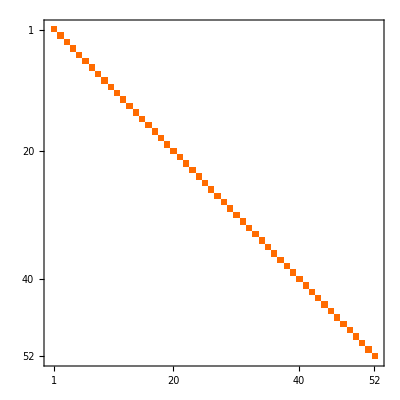
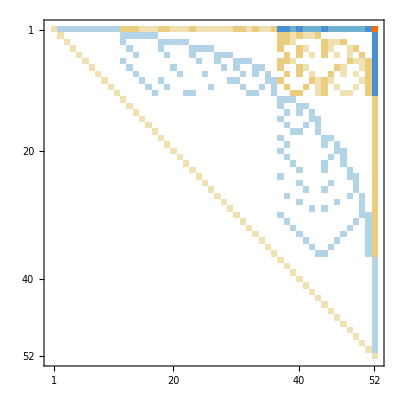
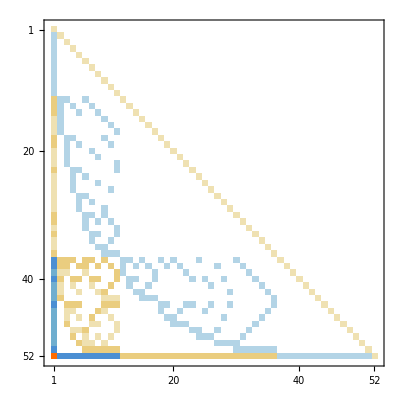
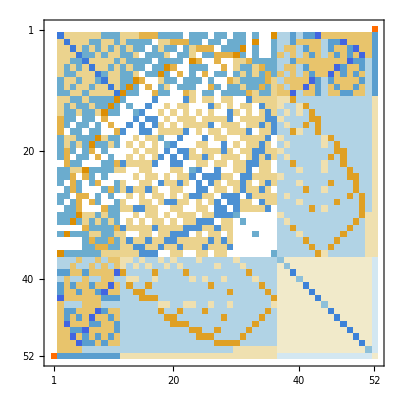
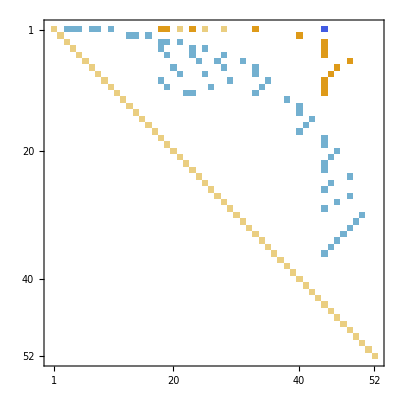
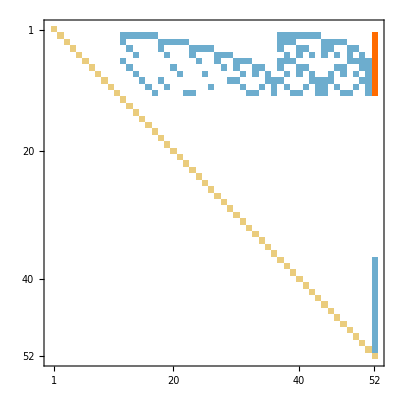
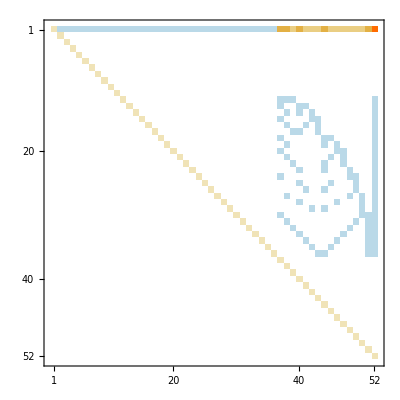
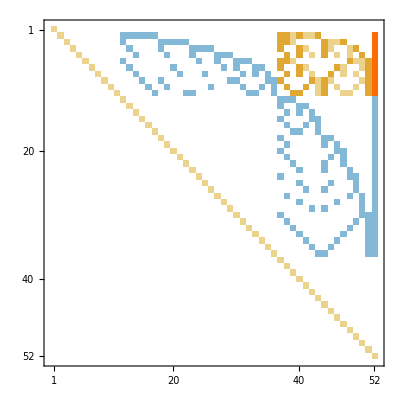
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T,-Graphics-C→Z,-Graphics-C→X,-Graphics-C→e},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T,-Graphics-E→Z,-Graphics-E→X,-Graphics-E→e},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T,-Graphics-G→Z,-Graphics-G→X,-Graphics-G→e},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T,-Graphics-F→Z,-Graphics-F→X,-Graphics-F→e},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T,-Graphics-T→Z,-Graphics-T→X,-Graphics-T→e},{-Graphics-Z→C,-Graphics-Z→E,-Graphics-Z→G,-Graphics-Z→F,-Graphics-Z→T,-Graphics-Z→Z,-Graphics-Z→X,-Graphics-Z→e},{-Graphics-X→C,-Graphics-X→E,-Graphics-X→G,-Graphics-X→F,-Graphics-X→T,-Graphics-X→Z,-Graphics-X→X,-Graphics-X→e},{-Graphics-e→C,-Graphics-e→E,-Graphics-e→G,-Graphics-e→F,-Graphics-e→T,-Graphics-e→Z,-Graphics-e→X,-Graphics-e→e}}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,Keys[Bases]},{base2,Keys[Bases]}]
```

```mathematica
Table[VertexCount[allGraphs5[k,"graph"]],{k,allGraphs5AtomKeys}]//Sort
```

{1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,5}

```mathematica
Table[Labeled[MatrixPlot[ConversionMatrix[base1,base2]],base1->base2],{base1,{"E","C","Z","X",letter}},{base2,{"E","C","Z","X",letter}}]//TableForm
```

-Graphics-E→E | -Graphics-E→C | -Graphics-E→Z | -Graphics-E→X | -Graphics-E→e
-Graphics-C→E | -Graphics-C→C | -Graphics-C→Z | -Graphics-C→X | -Graphics-C→e
-Graphics-Z→E | -Graphics-Z→C | -Graphics-Z→Z | -Graphics-Z→X | -Graphics-Z→e
-Graphics-X→E | -Graphics-X→C | -Graphics-X→Z | -Graphics-X→X | -Graphics-X→e
-Graphics-e→E | -Graphics-e→C | -Graphics-e→Z | -Graphics-e→X | -Graphics-e→e

```mathematica
(allGraphs5[lambdaKey,colofour]==0//Simplify)/.RepGraph[letter]
```

20 -Graphics-590481+5 -Graphics-582881+5 -Graphics-567701+-Graphics-560121+5 -Graphics-522321+-Graphics-499721+-Graphics-492201+2 -Graphics-514780+5 -Graphics-390141+-Graphics-326841+-Graphics-305861+5 -Graphics-298881+2 -Graphics-319840+2 -Graphics-368980+2 -Graphics-361940+2 -Graphics-383080+-Graphics-1312210+-Graphics-437410+-Graphics-16210+-Graphics-5410+-Graphics-610+-Graphics-295240==-Graphics-529745+2 -Graphics-439024+-Graphics-408785+-Graphics-393724+2 -Graphics-175144+-Graphics-48604+-Graphics-6665+-Graphics-132842+2 -Graphics-145864+2 -Graphics-5464+-Graphics-131762+-Graphics-131244+-Graphics-58345+-Graphics-16204+2 -Graphics-2184+-Graphics-44282+-Graphics-724+-Graphics-265+-Graphics-43802+-Graphics-1682

```mathematica
(allGraphs5[lambdaKey,colofour])/.RepGraph[letter]
```

20 -Graphics-590481+5 -Graphics-582881+5 -Graphics-567701+-Graphics-560121+5 -Graphics-522321+-Graphics-499721+-Graphics-492201+2 -Graphics-514780+5 -Graphics-390141+-Graphics-326841+-Graphics-305861+5 -Graphics-298881+2 -Graphics-319840+2 -Graphics-368980+2 -Graphics-361940+2 -Graphics-383080--Graphics-529745-2 -Graphics-439024--Graphics-408785--Graphics-393724-2 -Graphics-175144--Graphics-48604--Graphics-6665--Graphics-132842-2 -Graphics-145864-2 -Graphics-5464--Graphics-131762--Graphics-131244--Graphics-58345--Graphics-16204-2 -Graphics-2184--Graphics-44282--Graphics-724--Graphics-265--Graphics-43802--Graphics-1682+-Graphics-1312210+-Graphics-437410+-Graphics-16210+-Graphics-5410+-Graphics-610+-Graphics-295240

```mathematica
(allGraphs5[lambdaKey,colofour])//Length
```

42

```mathematica
(allGraphs5[alfaKey,colofour]//Simplify)/.RepGraph[letter]
```

3 -Graphics-590481+-Graphics-582881+-Graphics-567701+-Graphics-560121+2 -Graphics-390141--Graphics-529745--Graphics-175144--Graphics-145864--Graphics-131244+-Graphics-1312210

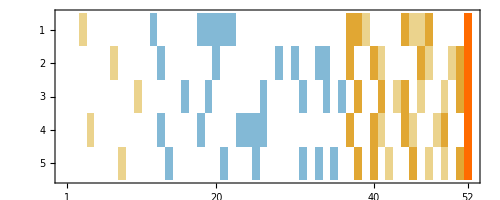

```mathematica
Table[(BaseCoeff[k,letter])/.RepGraph[letter],{k,quads}]//MatrixPlot
```

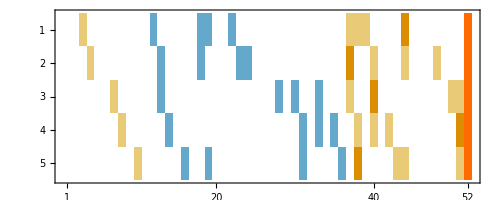

```mathematica
Table[(BaseCoeff[k,letter])/.RepGraph[letter],{k,alfas}]//MatrixPlot
```

```mathematica
allGraphs5[alfa1s//First,"colofour"]
```

v13x24x5

```mathematica
Bases["G","Colofour"]
```

colofourgenerator

```mathematica
Table[allGraphs5[k,"graph"]==(allGraphs5[k,"colofourgenerator"]/.RepGraph["G"]),{k,Join[quads,alfa1s,{lambdaKey}]}]//TableForm
```

-Graphics-==-Graphics-229630--Graphics-295240
-Graphics-==-Graphics-294430--Graphics-295240
-Graphics-==-Graphics-295210--Graphics-295240
-Graphics-==-Graphics-273370--Graphics-295240
-Graphics-==-Graphics-294970--Graphics-295240
-Graphics-==-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240
-Graphics-==-Graphics-273100--Graphics-294970--Graphics-273370+-Graphics-295240
-Graphics-==-Graphics-294400--Graphics-295210--Graphics-294430+-Graphics-295240
-Graphics-==-Graphics-229360--Graphics-294970--Graphics-229630+-Graphics-295240
-Graphics-==-Graphics-273340--Graphics-295210--Graphics-273370+-Graphics-295240
-Graphics-==-Graphics-294400+-Graphics-273340+-Graphics-273100+-Graphics-229360+-Graphics-228820--Graphics-295210--Graphics-294970--Graphics-294430--Graphics-273370--Graphics-229630+-Graphics-295240

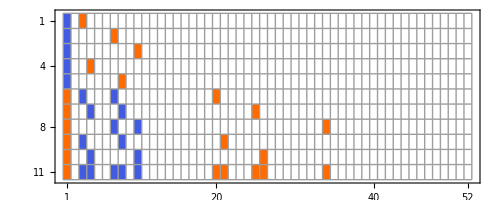

```mathematica
MatrixPlot[Table[(BaseCoeff[k,"G"]),{k,Join[quads,alfa1s,{lambdaKey}]}],Mesh->All,ImageSize->500]
```

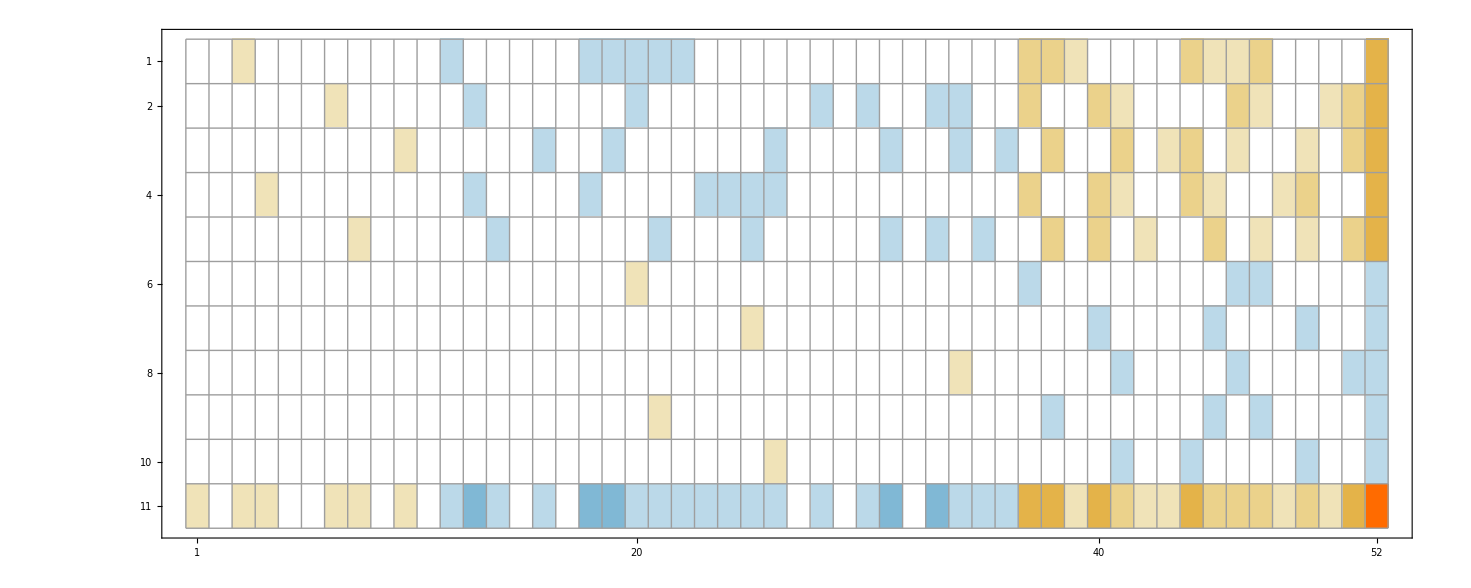

```mathematica
MatrixPlot[Table[(BaseCoeff[k,letter])/.RepGraph[letter],{k,Join[quads,alfa1s,{lambdaKey}]}],Mesh->All,ImageSize->500]
```

```mathematica
MatrixForm[Table[(BaseCoeff[k,letter])/.RepGraph[letter],{k,Join[quads,alfa1s,{lambdaKey}]}]]
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 1 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 2 | 0 | 0 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | -1 | -1 | 0 | 0 | 2 | 0 | 0 | 2 | 1 | 0 | 0 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 2 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | -1 | 0 | 2 | 0 | 0 | 2 | 0 | 1 | 2 | 0 | 1 | 0 | 0 | 1 | 0 | 2 | 5
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1 | -1 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 2 | 1 | 0 | 0 | 2 | 1 | 0 | 0 | 1 | 2 | 0 | 0 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | -1 | 0 | 0 | 2 | 0 | 2 | 0 | 1 | 0 | 0 | 2 | 0 | 1 | 0 | 1 | 0 | 2 | 5
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | -1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | -1 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | -1 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1 | 0 | 0 | 0 | 0 | -1 | 0 | 0 | -1
1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | -1 | -2 | -1 | 0 | -1 | 0 | -2 | -2 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 0 | -1 | 0 | -1 | -2 | 0 | -2 | -1 | -1 | -1 | 5 | 5 | 1 | 5 | 2 | 1 | 1 | 5 | 2 | 2 | 2 | 1 | 2 | 1 | 5 | 20)

```mathematica
Table[(allGraphs5[k,colofour]//Simplify)/.RepGraph[letter],{k,alfas}]//TableForm
```

3 -Graphics-590481+-Graphics-582881+-Graphics-567701+-Graphics-560121+2 -Graphics-390141--Graphics-529745--Graphics-175144--Graphics-145864--Graphics-131244+-Graphics-1312210
3 -Graphics-590481+2 -Graphics-582881+-Graphics-522321+-Graphics-390141+-Graphics-326841--Graphics-439024--Graphics-175144--Graphics-48604--Graphics-58345+-Graphics-437410
3 -Graphics-590481+-Graphics-582881+2 -Graphics-522321+-Graphics-305861+-Graphics-298881--Graphics-439024--Graphics-6665--Graphics-16204--Graphics-2184+-Graphics-16210
3 -Graphics-590481+-Graphics-567701+-Graphics-522321+-Graphics-499721+2 -Graphics-298881--Graphics-408785--Graphics-5464--Graphics-2184--Graphics-724+-Graphics-5410
3 -Graphics-590481+2 -Graphics-567701+-Graphics-492201+-Graphics-390141+-Graphics-298881--Graphics-393724--Graphics-145864--Graphics-5464--Graphics-265+-Graphics-610

```mathematica
Table[(allGraphs5[k,colofour]//Simplify)/.RepGraph[letter],{k,alfa1s}]//TableForm
```

--Graphics-590481--Graphics-582881--Graphics-368980--Graphics-361940+-Graphics-132842
--Graphics-590481--Graphics-522321--Graphics-319840--Graphics-383080+-Graphics-44282
--Graphics-590481--Graphics-514780--Graphics-298881--Graphics-368980+-Graphics-1682
--Graphics-590481--Graphics-567701--Graphics-361940--Graphics-383080+-Graphics-131762
--Graphics-590481--Graphics-514780--Graphics-390141--Graphics-319840+-Graphics-43802

```mathematica
ShowGraph5Least[alfa1Key]
```

-Graphics-361660

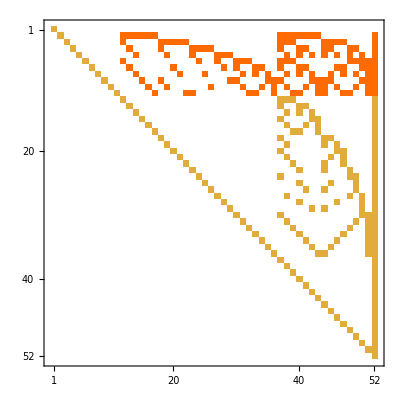
4 -Graphics-

```mathematica
MatrixPlot[ConversionMatrix[letter,"C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"]]4
```

```mathematica
MatrixPlot[ConversionMatrix[letter,"C"]]
```

-Graphics-

```mathematica
(ConversionMatrix["X","C"]-IdentityMatrix[52]+ConversionMatrix["Z","C"])==ConversionMatrix["E","C"]
```

True